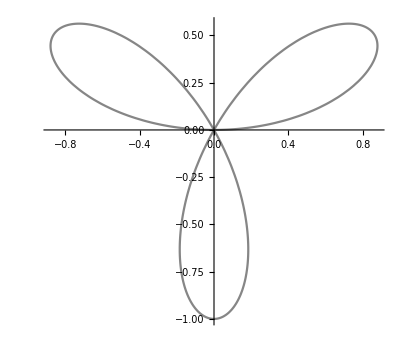

```mathematica
PolarPlot[Sin[3t],{t,0,π},ColorFunction->(Hue[#3]&)]
```

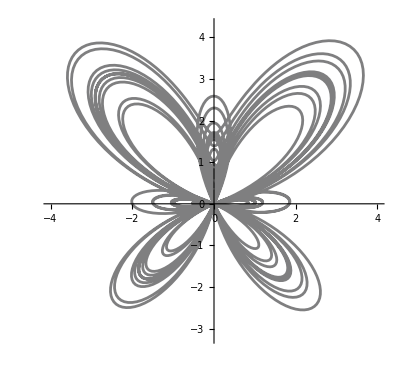

```mathematica
PolarPlot[ⅇ^Sin[θ]-2Cos[4θ]+Sin[θ/12]^5,{θ,0,24 π},PlotRange->{{-4,4},{-3.2,4.3}},PlotStyle->{Thickness[0.005],Black},ColorFunction->(Hue[#3]&)]
```

```mathematica
Manipulate[PolarPlot[ⅇ^Sin[θ]-c Cos[4θ]+d Sin[θ/12]^5,{θ,0,24 π},PlotRange->{{-4,4},{-3.2,4.3}},PlotStyle->{Thickness[0.005],Black},ColorFunction->(Hue[#1]&)],
{c,0,2},{d,{0,1}}]
```